```mathematica
On[Assert];
zi[eps_]:=(5-3 eps)/2;
phi[eps_]:=(3/2) (1+eps)^(1/3)(1-eps)^(2/3);
gamma[eps_]:=(1-eps)/2+Sqrt[1-eps^2];
psi[eps_]:=(1 - Log[(1+eps)/(1-eps)])^2(Log[2]/63);
beta[eps_]:=2^(2/3+psi[eps])phi[eps];
```

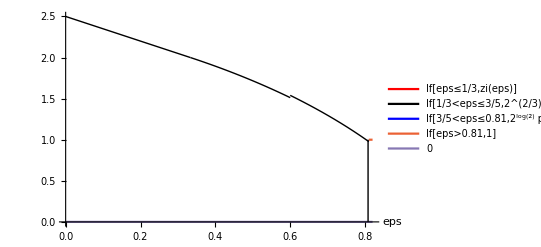

```mathematica
Plot[{
Style[If[eps ≤ 1/3,zi[eps]],Red],
Style[If[1/3 <eps ≤ 3/5,2^(2/3)phi[eps]],Black],
Style[If[3/5<eps≤ 0.81,2^(Log[2])phi[eps]],Blue],
If[eps >0.81,1],
0
(*Style[gamma[eps], Blue],
If[eps ≤ 0.81,2/3+psi[eps]]*)
},{eps, 0, 0.82}
,PlotLegends->"Expressions"
,AxesLabel->Automatic
,Epilog->{
Line[{{0.808,0},{0.808,1}}]
}
]
```

```mathematica
Manipulate[
Plot[{
(*Style[Log[2,(n^2/2)zi[eps]^n], Red],*)
(*Style[((n^2/2)zi[eps]^n)^(1/n), Black, Dashed],*)
(*Style[Log[phi[eps]^(2n)/9], Blue],*)
Style[(phi[eps]^2/zi[eps])^n 2/(9 n^2), Orange]
(*Style[Log[2,(n^2/2)zi[eps]^n - phi[eps]^(2n)/9], Black, Dashed]*)

},{eps, 0, 1/3}
,PlotRange->Full
]
,{n , 10, 200, 1},{delta, 0.1, 1}]
```

```mathematica
Manipulate[Plot[{
2^(n(2/3+deltaStar/2 + Log[2, 1-3 eps/5]/2 + Log[2,n]/n)),
2^(n(2/3+deltaStar/2 -0.43  eps+ Log[2,n]/n))
(*2^(n(deltaStar + 0.038))*)
},{eps, 0, 1/3}],{deltaStar, 1, 3, 0.01}, {n, 10, 100, 1}]
```

```mathematica
Manipulate[Plot[{
(phi[eps]^(2n)/9 )/((n^2)/2 beta[eps]^n)
},{eps, 1/3, 3/5}
],{n,10, 200,1}]
```

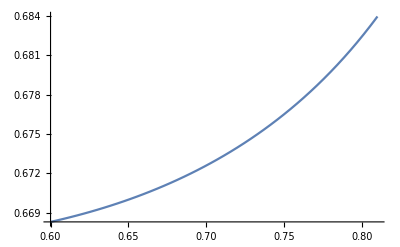

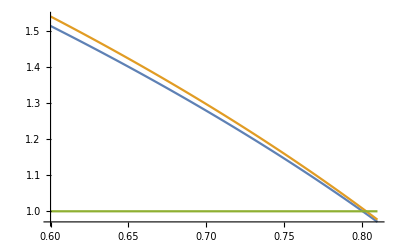

```mathematica
Plot[{2/3+psi[eps]},{eps, 0.6, 0.81}]
Plot[{
2^(2/3+psi[eps])phi[eps],
2^(Log[2]) phi[eps],
1
},{eps, 0.6, 0.81}]
```